Miembros del equipo:
· David Arnal García
· Luis Alberto Álvarez Zavaleta

# Práctica 2.2 - Reconocedores de Lenguajes

### Ejercicio 1

```mathematica
AFDToAC[afd_]:=Module[{S,Splus,delta,i,j,k},
S=afd[[1]]∪afd[[2]]; (* Q ∪ Σ *)
delta=afd[[3]]; (* δ *)
Splus=afd[[5]]; (* F *)
(* Inserting transitions ∀q,p ∈ Q -> f(q,p) = p *)
(* Inserting transitions ∀a,b ∈ ∑ -> f(a,b) = b *)
For[k=1,k≤2,++k,
For[i=1,i≤Length[afd[[k]]],++i,
For[j=1,j≤Length[afd[[k]]],++j,
AppendTo[delta,{afd[[k,i]],afd[[k,j]],afd[[k,j]]}];
];
];
];
Return[{S,delta,Splus}];
];
```

```mathematica
afd1={{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}};
AC1=AFDToAC[afd1]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

### Ejercicio 2

```mathematica
ACcheckString[string_,AC_,q_]:=Module[{res,i,j,aux},
res=string;
For[i=0,i<Length[res],++i,
(* aux = s -> Searching for: s = f(q, string[1] *)
aux={Cases[AC[[2]],{q,res[[1]],_}][[1,3]]};
For[j=1,j <Length[res],++j,
(* Appending to aux the state result of the transition *)
AppendTo[aux,Cases[AC[[2]],{res[[j]],res[[j+1]],_}][[1,3]]];
];
res=aux;
];
(* Checking if the last element of the last iteration of res is contained in S+ *)
Return[MemberQ[AC[[3]],res[[Length[string]]]]];
];
```

```mathematica
ACcheckString[{a,b,a,a,b},AC1,q]
```

True

### Ejercicio 3

```mathematica
AFDToBidirectionalAC[afd_]:=Module[{AC,newTransitions,i,j},
AC=AFDToAC[afd];
(* Converting all transitions {leftNeighbour, cell, newState} to transitions {leftNeighbour, cell, rightNeighbour, newState}, ∀rightNeighbour ∈ S *)
newTransitions={};
For[i=1,i≤Length[AC[[2]]],++i,
For[j=1,j≤Length[AC[[1]]],++j,
AppendTo[newTransitions,{AC[[2,i,1]],AC[[2,i,2]],AC[[1,j]],AC[[2,i,3]]}];
];
];
AC[[2]]=newTransitions;
Return[AC];
];
```

```mathematica
AFDToBidirectionalAC[afd1]
```

{{a,b,p,q,r},{{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r},{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b}},{r}}

### Ejercicio 4

```mathematica
ACToDiagram[string_,AC_,q_]:=Module[{res,i,j,aux,representation, assignedColours, colourAssignment, rules},
res=string;
representation = {string};
rules = AC[[2]];
For[i=0,i<Length[res],++i,
(* aux = s -> Searching for: s = f(q, string[1] *)
aux={Cases[rules,{q,res[[1]],_}][[1,3]]};
For[j=1,j <Length[res],++j,
(* Appending to aux the state result of the transition *)
AppendTo[aux,Cases[rules,{res[[j]],res[[j+1]],_}][[1,3]]];
];
PrependTo[representation,aux];
res=aux;
];

(* Assigning a colour to each state *)
assignedColours =RandomColor[Length[AC[[1]]]];
colourAssignment={};
For[i=1,i≤  Length[assignedColours],++i,
AppendTo[colourAssignment,AC[[1,i]]->assignedColours[[i]]];
];
Print[colourAssignment];
ArrayPlot[representation,ColorRules->colourAssignment, Mesh -> True]
];
```

{a→RGBColor[0.9768254944867478, 0.7737003708785506, 0.3185839062117146],b→RGBColor[0.28957483963260544, 0.5405957788304949, 0.7738369402534904],p→RGBColor[0.20347633357700357, 0.14073761112868866, 0.7159356653758304],q→RGBColor[0.757385220678449, 0.7343127095397393, 0.9254734847104533],r→RGBColor[0.6686689776804446, 0.31515562160786126, 0.6555103902545083]}

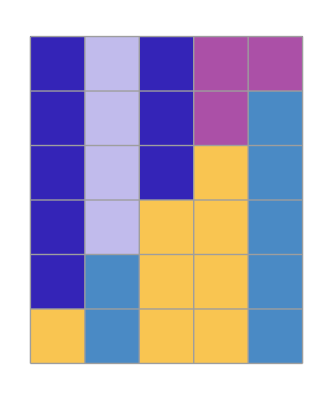

```mathematica
ACToDiagram[{a,b,a,a,b},AC1,q]
```